{27.1739,13.587,6.79348,3.39674,1.69837,0.849185,0.424592,0.}

{30.8642,15.4321,7.71605,3.85802,1.92901,0.964506,0.482253,0.}

{{27.1739,1},{13.587,0.974},{6.79348,0.926},{3.39674,0.839},{1.69837,0.687},{0.849185,0.424},{0.424592,0.159},{0.,0}}

{{30.8642,0.979},{15.4321,0.965},{7.71605,0.93},{3.85802,0.856},{1.92901,0.724},{0.964506,0.481},{0.482253,0.198},{0.,0}}

1.01787+0.275553/(0.512278+x)^3-0.510372/(0.512278+x)^2-0.575143/(0.512278+x)

0.994255+0.334711/(0.516634+x)^3-0.68094/(0.516634+x)^2-0.449649/(0.516634+x)

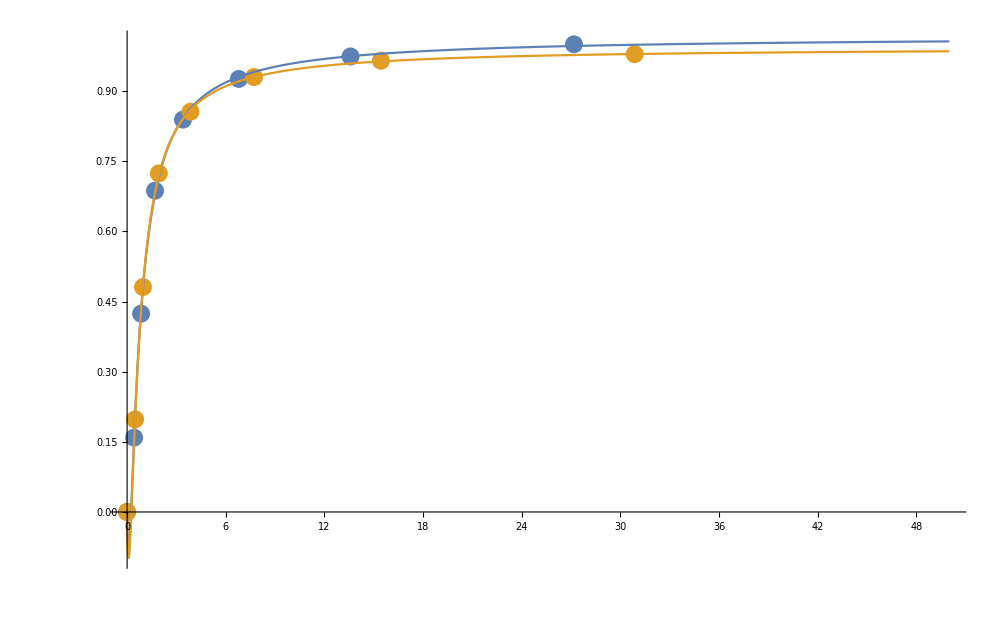

```mathematica
L={1/2,1/4,1/8,1/16,1/32,1/64,1/128,0}*1*10^-6;
a0=1.84*10^-8;
a1=1.62*10^-8;
mobwet0={1,0.974,0.926,0.839,0.687,0.424,0.159,0};
mobwet1={0.979,0.965,0.930,0.856,0.724,0.481,0.198,0};

ratio0=L/a0
ratio1=L/a1

curve0=Thread[{ratio0,mobwet0}]
curve1=Thread[{ratio1,mobwet1}]
fitfunc2=aa+bb 1/(x+ff)+cc 1/(x+ff)^2+dd 1/(x+ff)^3;
fit0[x_]=fitfunc2/. FindFit[ curve0,fitfunc2,{aa,bb,cc,dd,ee,ff},x]
fit1[x_]=fitfunc2/. FindFit[ curve1,fitfunc2,{aa,bb,cc,dd,ee,ff},x]

p1=ListPlot[{curve0,curve1},PlotRange->All];
p2=Plot[{fit0[x],fit1[x]},{x,0,50},PlotRange->All];
Show[p1,p2,PlotRange->All]
```

```mathematica
fit0[h]//FortranForm
```

1.0178739157211536 + 0.27555274006079666/(0.5122778234075493 + h)**3 - 0.5103722002042806/(0.5122778234075493 + h)**2 - 
     -  0.5751429346433427/(0.5122778234075493 + h)

```mathematica
fit0[13.547994145992023]
ratio[[2]]
```

0.974486

13.587

```mathematica
fit0[13.548]
```

0.972704

```mathematica
1.035599545901349 -(1.041441240367475/(1.068503148679744+h)  +2.217587383223687/(1.068503148679744+h)^2-7.595475420957568/(1.068503148679744+h)^3)/.h-> 13.547994145992023
```

0.956401

{27.1739,13.587,6.79348,3.39674,1.69837,0.849185,0.424592,0.}

{30.8642,15.4321,7.71605,3.85802,1.92901,0.964506,0.482253,0.}

{{27.1739,0.939},{13.587,0.913},{6.79348,0.83},{3.39674,0.68},{1.69837,0.442},{0.849185,0.2107},{0.424592,0.069},{0.,0}}

{{30.8642,0.95},{15.4321,0.929},{7.71605,0.858},{3.85802,0.723},{1.92901,0.492},{0.964506,0.248},{0.482253,0.0855},{0.,0}}

0.960379+8.06541/(1.60449+x)^3-6.93794/(1.60449+x)^2-0.34963/(1.60449+x)

0.966814+8.44903/(1.60949+x)^3-7.27482/(1.60949+x)^2-0.297612/(1.60949+x)

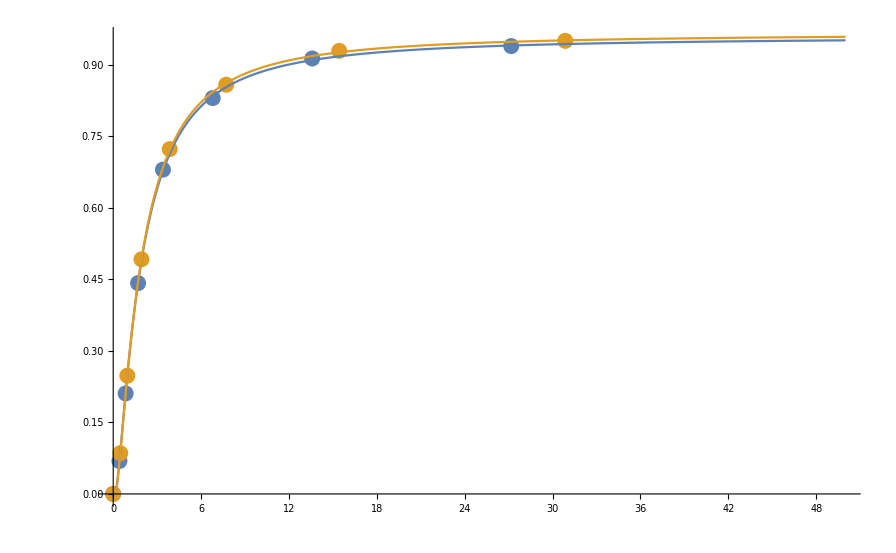

```mathematica
L={1/2,1/4,1/8,1/16,1/32,1/64,1/128,0}*1*10^-6;
a2=1.84*10^-8;
a3=1.62*10^-8;
mobwet2={0.939,0.913,0.830,0.680,0.442,0.2107,0.069,0};
mobwet3={0.95,0.929,0.858,0.723,0.492,0.248,0.0855,0};

ratio2=L/a2
ratio3=L/a3

curve2=Thread[{ratio2,mobwet2}]
curve3=Thread[{ratio3,mobwet3}]
fitfunc2=aa+bb 1/(x+ff)+cc 1/(x+ff)^2+dd 1/(x+ff)^3;
fit2[x_]=fitfunc2/. FindFit[ curve2,fitfunc2,{aa,bb,cc,dd,ee,ff},x]
fit3[x_]=fitfunc2/. FindFit[ curve3,fitfunc2,{aa,bb,cc,dd,ee,ff},x]

p3=ListPlot[{curve2,curve3},PlotRange->All];
p4=Plot[{fit2[x],fit3[x]},{x,0,50},PlotRange->All];
Show[p3,p4,PlotRange->All]
```

```mathematica
fit2[h]//FortranForm
```

0.9603792424884368 + 8.065409511535329/(1.6044917433014263 + h)**3 - 6.93794418399698/(1.6044917433014263 + h)**2 - 
     -  0.34962956857881305/(1.6044917433014263 + h)

```mathematica
fit2[0.84674963412450099]
```

0.21068